# Final

```mathematica
a=1;
b=1;
c=2;
```

```mathematica
V[x_]:=a Exp[b Tanh[c x]]
```

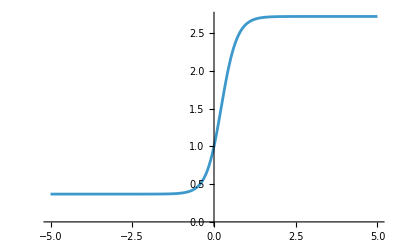

```mathematica
Plot[V[x],{x,-5,5}]
```

```mathematica
ϕ[z_]:=z^μ(1-z)^ν ω[z]
```

```mathematica
ϕ'[z]
```

(1-z)^ν z^(-1+μ) μ ω[z]-(1-z)^(-1+ν) z^μ ν ω[z]+(1-z)^ν z^μ ω'[z]

```mathematica
Simplify[((1-2 z)(1-z)z+2 μ (1-z) -2 μ z)/(z(1-z))]
```

-((-1+2 z) (-z+z^2-2 μ))/((-1+z) z)

```mathematica
z(1-z)(ω''[z]+2 (μ/z-ν/(1-z)))ω'[z]+((μ(μ-1))/z^2+(ν(ν-1))/(1-z)^2-(2 μ ν)/(z(1-z)))ω[z]+(1-2 z)(ω'[z]+(μ/z-ν/(1-z))ω[z])+(((E-V0  Exp[β z])^2-1)/(4 c^2 z (1-z)))ω[z]==0//Simplify
```

(((-1+μ) μ)/z^2+(2 μ ν)/((-1+z) z)+((-1+ν) ν)/(-1+z)^2) ω[z]+(1-2 z) ((μ/z+ν/(-1+z)) ω[z]+ω'[z])==((-1+(ⅇ-ⅇ^(z β) V0)^2) ω[z])/(16 (-1+z) z)+ω'[z] (2 (-1+z) μ+2 z ν+(-1+z) z ω''[z])

```mathematica
z(1-z)ω''[z]+(1-2 z +2 μ/z-(2 ν)/(1-z))ω'[z]+(((μ(μ-1))/z^2+(ν(ν-1))/(1-z)^2-(2 ν μ)/(z (1-z)))+(1-2z)(μ/z-ν/(1-z))+(K1/(4 c^2 z (1-z))))ω[z]==0//FullSimplify
```

K1 ω[z]+16 ((-1+z) (z (-1+2 z)-2 μ)-2 z ν) ω'[z]+16 (-1+z)^2 z^2 ω''[z]==(16 ((-1+z)^2 μ (-1+z-2 z^2+μ)+z (z (-2+(3-2 z) z)+2 (-1+z) μ) ν+z^2 ν^2) ω[z])/((-1+z) z)

```mathematica
(*Group terms carefully to show the structure*)structuredExpr=z (1-z) ω''[z]+Factor[1-2 z+(2 μ)/z-(2 ν)/(1-z)] ω'[z]+Factor[((μ (μ-1))/z^2+(ν (ν-1))/(1-z)^2-(2 μ ν)/(z (1-z)))+(1-2 z) (μ/z-ν/(1-z))+K1/(4 c^2 z (1-z))] ω[z]==0
```

-((-K1 z+K1 z^2+16 μ-48 z μ+80 z^2 μ-80 z^3 μ+32 z^4 μ-16 μ^2+32 z μ^2-16 z^2 μ^2+32 z^2 ν-48 z^3 ν+32 z^4 ν+32 z μ ν-32 z^2 μ ν-16 z^2 ν^2) ω[z])/(16 (-1+z)^2 z^2)-((z-3 z^2+2 z^3+2 μ-2 z μ-2 z ν) ω'[z])/((-1+z) z)+(1-z) z ω''[z]==0

## Matrix Numerical Method

```mathematica
(*Wave number and local potential*)k[x_,E_,m_,q_,a_,b_,c_]:=Sqrt[(E-q a Exp[b Tanh[c x]])^2-m^2]

(*Propagation through one slab*)
Sprop[k_,d_]:={{Exp[I k d],0},{0,Exp[-I k d]}};
```

```mathematica
Sinterface[kL_,kR_]:=Module[{t,r},t=2 kL/(kL+kR);(*transmission*)r=(kL-kR)/(kL+kR);(*reflection*){{1/t,-r/t},{-r/t,1/t}}]
```

```mathematica
If[Abs[kL + kR] < 10^-12, kR = kL + 10^-12];
```

```mathematica
Sstar[S1_,S2_]:=Module[{S11,S12,S21,S22,T11,T12,T21,T22,Iden},{{S11,S12},{S21,S22}}=S1;
{{T11,T12},{T21,T22}}=S2;
Iden=IdentityMatrix[1];
{{S11+S12.Inverse[Iden-T11.S22].T11.S21,S12.Inverse[Iden-T11.S22].T12},{T21.Inverse[Iden-S22.T11].S21,T22+T21.Inverse[Iden-S22.T11].S22.T12}}]
```

```mathematica
FullScatteringMatrix[E_,m_,q_,a_,b_,c_,L_,N_]:=Module[{xs,dx,mids,ks,S,Sj},xs=Subdivide[-L,L,N];
dx=xs[[2]]-xs[[1]];
mids=Most@MovingAverage[xs,2];
ks=k[#,E,m,q,a,b,c]&/@mids;
(*start with identity S-matrix*)S={{1,0},{0,1}};
Do[Sj=Sinterface[If[Abs[ks[[j]]]<10^-8,10^-8,ks[[j]]],If[j<N,ks[[j+1]],ks[[j]]]];
S=Sstar[S,Sj];
S=Sstar[S,Sprop[ks[[j]],dx]];,{j,1,N}];
S]
```

```mathematica
ScatteringCoefficientsStable[E_,m_,q_,a_,b_,c_,L_,N_]:=Module[{S,t,r,km,kp,OmM,OmP,vminus,vplus},S=FullScatteringMatrix[E,m,q,a,b,c,L,N];
t=1/S[[1,1]];
r=S[[2,1]]/S[[1,1]];
OmM=E-q a Exp[-b];
OmP=E-q a Exp[b];
km=Sqrt[OmM^2-m^2];
kp=Sqrt[OmP^2-m^2];
vminus=Re[km/OmM];
vplus=Re[kp/OmP];
{Abs[r]^2,(vplus/vminus) Abs[t]^2}]
```

```mathematica
Manipulate[Module[{energies,vals,Rvals,Tvals},energies=Subdivide[Emin,Emax,200];
vals=ScatteringCoefficientsStable[#,m,q,a,b,c,L,Nsteps]&/@energies;
Rvals=vals[[All,1]];
Tvals=vals[[All,2]];
ListLinePlot[{Transpose[{energies,Rvals}],Transpose[{energies,Tvals}]},PlotRange->All,Frame->True,PlotLegends->{"R(E)","T(E)"},PlotStyle->{Blue,Red},ImageSize->Large]],{{a,1.0},0.1,3},{{b,1.0},-3,3},{{c,1.0},0.05,2},{{m,1.0},0.1,3},{{q,1.0},0.1,3},{{Emin,-3},-10,0},{{Emax,3},0,10},{{L,20},5,50},{{Nsteps,200},20,1500,20}]
```